```mathematica
(*propfac=0.4*)
J2Prop=Simplify[Sqrt[J2Sig]/.{sig1->siga,sig2->sigr,sig3->sigr},Assumptions->{siga-sigr<0}]
I1Prop=I1Sig/.{sig1->siga,sig2->sigr,sig3->sigr}
sol=Solve[{J2Prop==J2Val,I1Prop==I1Val},{siga,sigr}]
siga-sigr/.sol[[1]]//Simplify
Clear[propfac,sol]
```

(-siga+sigr)/(√3)

siga+2 sigr

{{siga→(√3 I1Val-6 J2Val)/(3 √3),sigr→I1Val/3+J2Val/(√3)}}

-√3 J2Val

```mathematica
I1SqJ2[point_]:={√3 point[[1]],1/√2 point[[2]]}
```

```mathematica
(*propfac=0.4*)
J2Prop=Simplify[Sqrt[J2Sig]/.{sig1->siga,sig2->sigr,sig3->sigr},Assumptions->{siga<0,sigr<0,siga<sigr}]
I1Prop=I1Sig/.{sig1->siga,sig2->sigr,sig3->sigr}
```

(-siga+sigr)/(√3)

siga+2 sigr

```mathematica
Function1[I1Prop,J2Prop]
```

-0.25+0.18 ⅇ^(0.67 (siga+2 sigr))+(-siga+sigr)/(√3)

```mathematica
FindRoot[Function1[I1Prop,J2Prop]//.{siga->sigr-x,sigr->-0.1},{x,0.25}]
```

{x→0.21174}

```mathematica
Function1[I1Prop,J2Prop]//.{siga->sigr-x,sigr->-0.8}/.x->0.384759
```

5.34126×10^-8

```mathematica
IJ2=Table[{I1Prop,J2Prop,-√3 J2Prop},{siga,sigr,sigr-0.38,(-0.38-0.001)/40}]/.sigr->-0.8
IJ2AdjustEpsp[IJ_]:=Block[{lij,f2,epsp,i,tabepsp},
lij=Length[IJ];
tabepsp=Table[0,{lij}];
epsp=0;

For[i=1,i≤lij,i++,
f2=Function2[IJ[[i,1]],IJ[[i,2]],epsp];
If[f2>0,
epsp=SolveFunction2Epsp[IJ[[i,1]],IJ[[i,2]],epsp];
tabepsp[[i]]=epsp
,tabepsp[[i]]=epsp]
];
tabepsp
]
Table[{Function1[IJ2[[i,1]],IJ2[[i,2]]],Function2[IJ2[[i,1]],IJ2[[i,2]],0]},{i,1,Length[IJ2]}]
TabEpsp=IJ2AdjustEpsp[IJ2]
Table[Function2[IJ2[[i,1]],IJ2[[i,2]],TabEpsp[[i]]],{i,1,Length[IJ2]}]
Table[TabEpsp[[i+1]]-TabEpsp[[i]],{i,1,Length[TabEpsp]-1}]
```

{{-2.4,0,0},{-2.40953,0.00549926,-0.009525},{-2.41905,0.0109985,-0.01905},{-2.42858,0.0164978,-0.028575},{-2.4381,0.021997,-0.0381},{-2.44763,0.0274963,-0.047625},{-2.45715,0.0329956,-0.05715},{-2.46668,0.0384948,-0.066675},{-2.4762,0.0439941,-0.0762},{-2.48573,0.0494934,-0.085725},{-2.49525,0.0549926,-0.09525},{-2.50478,0.0604919,-0.104775},{-2.5143,0.0659911,-0.1143},{-2.52383,0.0714904,-0.123825},{-2.53335,0.0769897,-0.13335},{-2.54288,0.0824889,-0.142875},{-2.5524,0.0879882,-0.1524},{-2.56193,0.0934874,-0.161925},{-2.57145,0.0989867,-0.17145},{-2.58098,0.104486,-0.180975},{-2.5905,0.109985,-0.1905},{-2.60003,0.115484,-0.200025},{-2.60955,0.120984,-0.20955},{-2.61908,0.126483,-0.219075},{-2.6286,0.131982,-0.2286},{-2.63813,0.137482,-0.238125},{-2.64765,0.142981,-0.24765},{-2.65718,0.14848,-0.257175},{-2.6667,0.153979,-0.2667},{-2.67623,0.159479,-0.276225},{-2.68575,0.164978,-0.28575},{-2.69528,0.170477,-0.295275},{-2.7048,0.175976,-0.3048},{-2.71433,0.181476,-0.314325},{-2.72385,0.186975,-0.32385},{-2.73338,0.192474,-0.333375},{-2.7429,0.197973,-0.3429},{-2.75243,0.203473,-0.352425},{-2.76195,0.208972,-0.36195},{-2.77148,0.214471,-0.371475}}

{{-0.213948,361.485},{-0.208678,364.227},{-0.203407,367.},{-0.198134,369.805},{-0.19286,372.642},{-0.187584,375.51},{-0.182307,378.41},{-0.177028,381.342},{-0.171749,384.305},{-0.166467,387.3},{-0.161184,390.326},{-0.1559,393.384},{-0.150615,396.474},{-0.145328,399.595},{-0.14004,402.748},{-0.13475,405.932},{-0.129459,409.148},{-0.124167,412.396},{-0.118874,415.675},{-0.113579,418.986},{-0.108283,422.328},{-0.102985,425.702},{-0.0976868,429.108},{-0.0923868,432.545},{-0.0870856,436.014},{-0.0817831,439.515},{-0.0764794,443.047},{-0.0711744,446.61},{-0.0658682,450.206},{-0.0605607,453.833},{-0.0552521,457.491},{-0.0499422,461.181},{-0.0446311,464.903},{-0.0393188,468.656},{-0.0340053,472.441},{-0.0286907,476.258},{-0.0233749,480.106},{-0.0180579,483.986},{-0.0127397,487.897},{-0.0074204,491.84}}

{-0.052781,-0.0528668,-0.0529553,-0.0530464,-0.0531402,-0.0532366,-0.0533354,-0.0534367,-0.0535404,-0.0536465,-0.0537549,-0.0538656,-0.0539786,-0.0540939,-0.0542114,-0.0543311,-0.0544532,-0.0545775,-0.054704,-0.0548329,-0.0549642,-0.0550978,-0.0552339,-0.0553726,-0.0555139,-0.0556581,-0.0558052,-0.0559555,-0.0561092,-0.0562666,-0.0564282,-0.0565944,-0.0567659,-0.0569435,-0.0571285,-0.0573226,-0.0575282,-0.0577497,-0.0579945,-0.0582796}

{2.22045×10^-16,-2.22045×10^-16,-5.55112×10^-16,8.88178×10^-16,3.10862×10^-15,2.22045×10^-16,1.11022×10^-15,1.88738×10^-15,-1.33227×10^-15,-8.88178×10^-16,-1.11022×10^-15,-3.33067×10^-16,-3.33067×10^-16,-7.77156×10^-16,2.22045×10^-16,-2.9976×10^-15,3.33067×10^-16,2.22045×10^-16,-5.55112×10^-16,6.66134×10^-16,3.33067×10^-16,1.9984×10^-15,1.66533×10^-15,4.44089×10^-16,5.55112×10^-16,-2.33147×10^-15,5.55112×10^-16,-1.66533×10^-15,-1.94289×10^-15,1.05471×10^-15,5.55112×10^-17,1.4988×10^-15,-1.60982×10^-15,-4.44089×10^-16,4.71845×10^-16,1.11022×10^-15,9.15934×10^-16,-4.71845×10^-16,-1.11022×10^-16,9.02056×10^-17}

{-0.0000857558,-0.000088499,-0.0000911742,-0.0000937864,-0.0000963405,-0.0000988412,-0.000101293,-0.000103702,-0.000106072,-0.000108408,-0.000110715,-0.000112999,-0.000115266,-0.000117521,-0.000119772,-0.000122025,-0.000124288,-0.000126571,-0.000128884,-0.000131236,-0.000133643,-0.000136118,-0.000138679,-0.000141348,-0.00014415,-0.000147116,-0.000150284,-0.000153703,-0.000157435,-0.000161562,-0.000166194,-0.000171481,-0.000177641,-0.000184997,-0.000194057,-0.000205679,-0.000221457,-0.00024481,-0.00028507}

```mathematica
AllDeriv=Table[Derivatives[IJ2[[i]],(IJ2[[2]]-IJ2[[1]]),TabEpsp[[i]]],{i,1,Length[IJ2]}]
FirstDeform={{{IJ2[[1,1]]/(K√3),IJ2[[1,2]]/(2 G)},{0,0},TabEpsp[[1]]}}/.exemple
For[i=1,i<Length[AllDeriv],i++,
AppendTo[FirstDeform,FirstDeform[[i]]+(AllDeriv[[i]]+AllDeriv[[i+1]])/2]
]
```

{{{-0.0000963305,0.0000972141},{-0.0000487055,0.},-0.0000843603},{{-0.0000979348,0.000098627},{-0.0000503098,1.41286×10^-6},-0.0000871392},{{-0.0000994985,0.000100126},{-0.0000518735,2.91231×10^-6},-0.0000898475},{{-0.000101024,0.000101712},{-0.0000533994,4.49823×10^-6},-0.0000924904},{{-0.000102515,0.000103385},{-0.0000548903,6.17119×10^-6},-0.0000950727},{{-0.000103974,0.000105147},{-0.000056349,7.93246×10^-6},-0.0000975993},{{-0.000105403,0.000106998},{-0.0000577783,9.78407×10^-6},-0.000100075},{{-0.000106806,0.000108943},{-0.000059181,0.0000117288},-0.000102505},{{-0.000108185,0.000110984},{-0.0000605599,0.0000137702},-0.000104893},{{-0.000109543,0.000113127},{-0.0000619178,0.0000159128},-0.000107245},{{-0.000110883,0.000115376},{-0.0000632577,0.0000181621},-0.000109565},{{-0.000112208,0.000117739},{-0.0000645825,0.0000205247},-0.00011186},{{-0.000113521,0.000120223},{-0.0000658956,0.0000230085},-0.000114135},{{-0.000114825,0.000122837},{-0.0000672004,0.0000256228},-0.000116395},{{-0.000116126,0.000125593},{-0.0000685005,0.0000283787},-0.000118646},{{-0.000117425,0.000128503},{-0.0000697999,0.0000312891},-0.000120897},{{-0.000118728,0.000131584},{-0.000071103,0.0000343695},-0.000123154},{{-0.00012004,0.000134852},{-0.0000724146,0.000037638},-0.000125426},{{-0.000121365,0.00013833},{-0.0000737401,0.0000411164},-0.000127722},{{-0.000122711,0.000142044},{-0.0000750856,0.0000448303},-0.000130052},{{-0.000124083,0.000146025},{-0.0000764581,0.0000488108},-0.000132429},{{-0.000125491,0.000150309},{-0.0000778657,0.0000530953},-0.000134867},{{-0.000126943,0.000154943},{-0.0000793177,0.0000577294},-0.000137382},{{-0.00012845,0.000159983},{-0.0000808254,0.0000627691},-0.000139994},{{-0.000130027,0.000165498},{-0.0000824019,0.0000682841},-0.000142724},{{-0.000131689,0.000171576},{-0.0000840636,0.0000743617},-0.000145602},{{-0.000133455,0.000178328},{-0.0000858302,0.0000811136},-0.000148662},{{-0.000135352,0.000185898},{-0.0000877265,0.000088684},-0.000151947},{{-0.000137409,0.000194477},{-0.0000897842,0.0000972631},-0.000155511},{{-0.000139669,0.000204321},{-0.000092044,0.000107107},-0.000159425},{{-0.000142185,0.000215783},{-0.0000945601,0.000118569},-0.000163783},{{-0.000145031,0.000229364},{-0.0000974063,0.00013215},-0.000168713},{{-0.000148311,0.000245802},{-0.000100686,0.000148588},-0.000174393},{{-0.000152175,0.000266231},{-0.00010455,0.000169017},-0.000181085},{{-0.000156852,0.000292486},{-0.000109227,0.000195272},-0.000189187},{{-0.000162715,0.000327758},{-0.00011509,0.000230544},-0.000199343},{{-0.000170417,0.000378139},{-0.000122792,0.000280924},-0.000212682},{{-0.000181235,0.000456914},{-0.00013361,0.0003597},-0.00023142},{{-0.000198146,0.000599784},{-0.000150521,0.00050257},-0.00026071},{{-0.000230534,0.000947127},{-0.000182909,0.000849913},-0.000316808}}

{{{-0.0207846,0},{0,0},-0.052781}}

{-0.052781,-0.0528668,-0.0529552,-0.0530464,-0.0531402,-0.0532365,-0.0533354,-0.0534367,-0.0535404,-0.0536464,-0.0537548,-0.0538655,-0.0539785,-0.0540938,-0.0542113,-0.0543311,-0.0544531,-0.0545774,-0.054704,-0.0548329,-0.0549641,-0.0550978,-0.0552339,-0.0553726,-0.0555139,-0.0556581,-0.0558052,-0.0559555,-0.0561093,-0.0562667,-0.0564283,-0.0565946,-0.0567661,-0.0569439,-0.057129,-0.0573233,-0.0575293,-0.0577513,-0.0579974,-0.0582862}

{-0.052781,-0.0528668,-0.0529553,-0.0530464,-0.0531402,-0.0532366,-0.0533354,-0.0534367,-0.0535404,-0.0536465,-0.0537549,-0.0538656,-0.0539786,-0.0540939,-0.0542114,-0.0543311,-0.0544532,-0.0545775,-0.054704,-0.0548329,-0.0549642,-0.0550978,-0.0552339,-0.0553726,-0.0555139,-0.0556581,-0.0558052,-0.0559555,-0.0561092,-0.0562666,-0.0564282,-0.0565944,-0.0567659,-0.0569435,-0.0571285,-0.0573226,-0.0575282,-0.0577497,-0.0579945,-0.0582796}

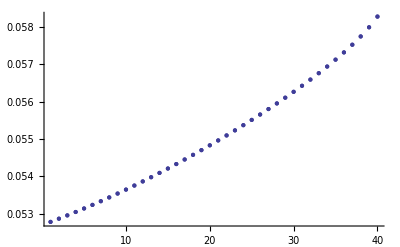

```mathematica
epsp=Table[FirstDeform[[i,3]],{i,Length[FirstDeform]}]
TabEpsp
ga=ListPlot[-epsp];
gb=ListPlot[-TabEpsp];
Show[ga,gb]
Clear[ga,gb]
```

{{{-0.0207846,0},{0,0},-0.052781},{{-0.0208817,0.0000979206},{-0.0000495076,7.06429×10^-7},-0.0528668},{{-0.0209805,0.000197297},{-0.000100599,2.86901×10^-6},-0.0529552},{{-0.0210807,0.000298217},{-0.000153236,6.57428×10^-6},-0.0530464},{{-0.0211825,0.000400765},{-0.000207381,0.000011909},-0.0531402},{{-0.0212857,0.000505031},{-0.000263,0.0000189608},-0.0532365},{{-0.0213904,0.000611104},{-0.000320064,0.0000278191},-0.0533354},{{-0.0214965,0.000719074},{-0.000378544,0.0000385755},-0.0534367},{{-0.021604,0.000829038},{-0.000438414,0.000051325},-0.0535404},{{-0.0217129,0.000941094},{-0.000499653,0.0000661665},-0.0536464},{{-0.0218231,0.00105535},{-0.000562241,0.0000832039},-0.0537548},{{-0.0219346,0.0011719},{-0.000626161,0.000102547},-0.0538655},{{-0.0220475,0.00129088},{-0.0006914,0.000124314},-0.0539785},{{-0.0221617,0.00141241},{-0.000757948,0.00014863},-0.0540938},{{-0.0222772,0.00153663},{-0.000825798,0.00017563},-0.0542113},{{-0.0223939,0.00166368},{-0.000894949,0.000205464},-0.0543311},{{-0.022512,0.00179372},{-0.0009654,0.000238294},-0.0544531},{{-0.0226314,0.00192694},{-0.00103716,0.000274297},-0.0545774},{{-0.0227521,0.00206353},{-0.00111024,0.000313675},-0.054704},{{-0.0228741,0.00220372},{-0.00118465,0.000356648},-0.0548329},{{-0.0229975,0.00234775},{-0.00126042,0.000403469},-0.0549641},{{-0.0231223,0.00249592},{-0.00133758,0.000454422},-0.0550978},{{-0.0232485,0.00264854},{-0.00141617,0.000509834},-0.0552339},{{-0.0233762,0.00280601},{-0.00149625,0.000570083},-0.0553726},{{-0.0235055,0.00296875},{-0.00157786,0.00063561},-0.0555139},{{-0.0236363,0.00313729},{-0.00166109,0.000706933},-0.0556581},{{-0.0237689,0.00331224},{-0.00174604,0.00078467},-0.0558052},{{-0.0239033,0.00349435},{-0.00183282,0.000869569},-0.0559555},{{-0.0240397,0.00368454},{-0.00192157,0.000962543},-0.0561093},{{-0.0241782,0.00388394},{-0.00201249,0.00106473},-0.0562667},{{-0.0243191,0.00409399},{-0.00210579,0.00117757},-0.0564283},{{-0.0244628,0.00431656},{-0.00220177,0.00130292},-0.0565946},{{-0.0246094,0.00455415},{-0.00230082,0.00144329},-0.0567661},{{-0.0247597,0.00481016},{-0.00240344,0.0016021},-0.0569439},{{-0.0249142,0.00508952},{-0.00251032,0.00178424},-0.057129},{{-0.025074,0.00539964},{-0.00262248,0.00199715},-0.0573233},{{-0.0252405,0.00575259},{-0.00274142,0.00225288},-0.0575293},{{-0.0254164,0.00617012},{-0.00286963,0.0025732},-0.0577513},{{-0.0256061,0.00669847},{-0.00301169,0.00300433},-0.0579974},{{-0.0258204,0.00747192},{-0.00317841,0.00368057},-0.0582862}}

{{0,0},{-0.000119928,-0.009525},{-0.000241639,-0.01905},{-0.000365239,-0.028575},{-0.000490835,-0.0381},{-0.000618535,-0.047625},{-0.000748446,-0.05715},{-0.000880683,-0.066675},{-0.00101536,-0.0762},{-0.0011526,-0.085725},{-0.00129253,-0.09525},{-0.00143528,-0.104775},{-0.001581,-0.1143},{-0.00172985,-0.123825},{-0.00188198,-0.13335},{-0.00203758,-0.142875},{-0.00219685,-0.1524},{-0.00236001,-0.161925},{-0.0025273,-0.17145},{-0.00269899,-0.180975},{-0.0028754,-0.1905},{-0.00305686,-0.200025},{-0.00324379,-0.20955},{-0.00343664,-0.219075},{-0.00363596,-0.2286},{-0.00384237,-0.238125},{-0.00405665,-0.24765},{-0.00427969,-0.257175},{-0.00451262,-0.2667},{-0.00475683,-0.276225},{-0.00501409,-0.28575},{-0.00528669,-0.295275},{-0.00557767,-0.3048},{-0.00589122,-0.314325},{-0.00623336,-0.32385},{-0.00661319,-0.333375},{-0.00704546,-0.3429},{-0.00755682,-0.352425},{-0.00820391,-0.36195},{-0.0091512,-0.371475}}

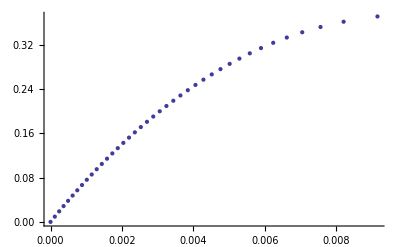

```mathematica
FirstDeform
epssig=Table[{-FirstDeform[[i,1,2]]Sqrt[3/2],IJ2[[i,3]]},{i,1,Length[FirstDeform]}]
ListPlot[-epssig]
```

```mathematica
Fig14J2Plot[sigrarg_,delsigmax_]:=Block[{J2Prop,I1Prop,IJ2,TabEpsp,AllDeriv,FirstDeform,epssig,Pr},
Pr=False;
J2Prop=Simplify[Sqrt[J2Sig]/.{sig1->siga,sig2->sigr,sig3->sigr},Assumptions->{siga<0,sigr<0,siga<sigr}];
I1Prop=I1Sig/.{sig1->siga,sig2->sigr,sig3->sigr};
IJ2=Table[{I1Prop,J2Prop,-√3 J2Prop},{siga,sigr,sigr-delsigmax,-(delsigmax-10^-6)/40}]/.sigr->-sigrarg;
If[Pr,Print["IJ2 = ",IJ2]];
TabEpsp=IJ2AdjustEpsp[IJ2];
If[Pr,Print["TabEpsp = ",TabEpsp]];
AllDeriv=Table[Derivatives[IJ2[[i]],(IJ2[[2]]-IJ2[[1]]),TabEpsp[[i]]],{i,1,Length[IJ2]}];
FirstDeform={{{IJ2[[1,1]]/(K√3),IJ2[[1,2]]/(2 G)},{0,0},TabEpsp[[1]]}}/.exemple;
For[i=1,i<Length[AllDeriv],i++,
AppendTo[FirstDeform,FirstDeform[[i]]+(AllDeriv[[i]]+AllDeriv[[i+1]])/2]
];
epssig=Table[{-FirstDeform[[i,1,2]]Sqrt[3/2],IJ2[[i,3]]},{i,1,Length[FirstDeform]}];
epssig
]
```

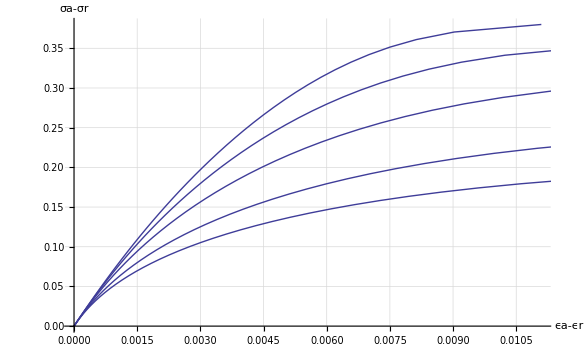

```mathematica
aeps=Fig14J2Plot[0.8,0.38];
beps=Fig14J2Plot[0.6,0.35];
ceps=Fig14J2Plot[0.4,0.32];
deps=Fig14J2Plot[0.2,0.256];
feps=Fig14J2Plot[0.1,0.211];
ga=ListPlot[-aeps,PlotJoined->True];
gb=ListPlot[-beps,PlotJoined->True];
gc=ListPlot[-ceps,PlotJoined->True];
gd=ListPlot[-deps,PlotJoined->True];
ge=ListPlot[-feps,PlotJoined->True];
Show[ga,gb,gc,gd,ge,AxesLabel->{"ϵa-ϵr","σa-σr"},GridLines->Automatic]
```

```mathematica
Fig14EpsaPlot[sigrarg_,delsigmax_]:=Block[{J2Prop,I1Prop,IJ2,TabEpsp,AllDeriv,FirstDeform,epssig,Pr,epsvec},
Pr=False;
J2Prop=Simplify[Sqrt[J2Sig]/.{sig1->siga,sig2->sigr,sig3->sigr},Assumptions->{siga<0,sigr<0,siga<sigr}];
I1Prop=I1Sig/.{sig1->siga,sig2->sigr,sig3->sigr};
IJ2=Table[{I1Prop,J2Prop,-√3 J2Prop},{siga,sigr,sigr-delsigmax,-(delsigmax-10^-6)/40}]/.sigr->-sigrarg;
If[Pr,Print["IJ2 = ",IJ2]];
TabEpsp=IJ2AdjustEpsp[IJ2];
If[Pr,Print["TabEpsp = ",TabEpsp]];
AllDeriv=Table[Derivatives[IJ2[[i]],(IJ2[[2]]-IJ2[[1]]),TabEpsp[[i]]],{i,1,Length[IJ2]}];
FirstDeform={{{IJ2[[1,1]]/(K√3),IJ2[[1,2]]/(2 G)},{0,0},TabEpsp[[1]]}}/.exemple;
For[i=1,i<Length[AllDeriv],i++,
AppendTo[FirstDeform,FirstDeform[[i]]+(AllDeriv[[i]]+AllDeriv[[i+1]])/2]
];
epssig=Table[{FirstDeform[[i,1,1]]/Sqrt[3]-FirstDeform[[i,1,2]]Sqrt[2/3],IJ2[[i,3]]},{i,1,Length[FirstDeform]}];
epssig
]
```

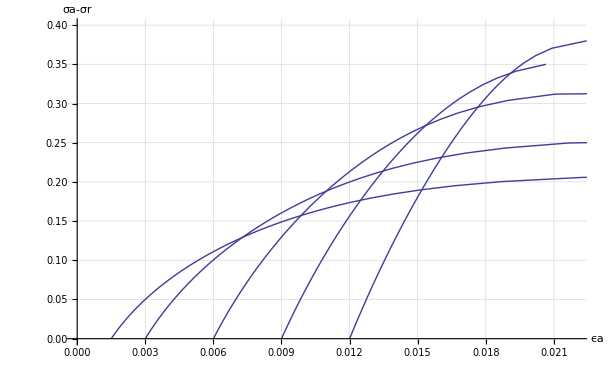

```mathematica
aeps=Fig14EpsaPlot[0.8,0.38];
beps=Fig14EpsaPlot[0.6,0.35];
ceps=Fig14EpsaPlot[0.4,0.32];
deps=Fig14EpsaPlot[0.2,0.256];
feps=Fig14EpsaPlot[0.1,0.211];
ga=ListPlot[-aeps,PlotJoined->True];
gb=ListPlot[-beps,PlotJoined->True];
gc=ListPlot[-ceps,PlotJoined->True];
gd=ListPlot[-deps,PlotJoined->True];
ge=ListPlot[-feps,PlotJoined->True];
Show[ge,ga,gb,gc,gd,PlotRange->{{0,0.022},{0,0.4}},AxesLabel->{"ϵa","σa-σr"},GridLines->Automatic]
```

```mathematica
sub1=siga->(√3 I1Val-6 J2Val)/(3 √3)
sub2={I1Val->I1SqJ2[{p1,p2}][[1]],J2Val->I1SqJ2[{p1,p2}][[2]]}
sub1/.sub2//Simplify
```

siga→(√3 I1Val-6 J2Val)/(3 √3)

{I1Val→√3 p1,J2Val→p2/(√2)}

siga→(p1-√2 p2)/(√3)

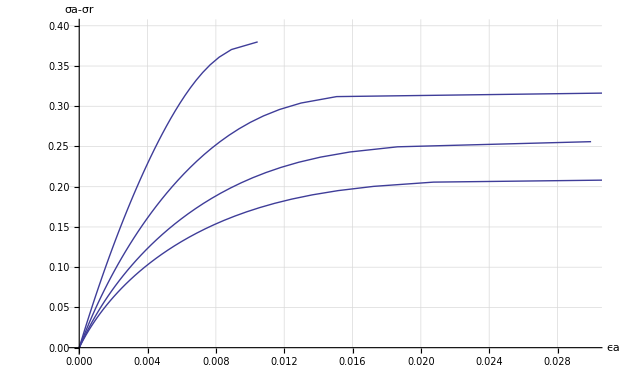

```mathematica
TranslateFig[al_]:=Block[{x,l,res,i},
x=al[[1,1]];
l=Length[al];
res=al;
For[i=1,i≤l,i++,res[[i,1]]-=x];
res
]

aeps=TranslateFig[Fig14EpsaPlot[0.8,0.38]];
beps=TranslateFig[Fig14EpsaPlot[0.6,0.35]];
ceps=TranslateFig[Fig14EpsaPlot[0.4,0.32]];
deps=TranslateFig[Fig14EpsaPlot[0.2,0.256]];
feps=TranslateFig[Fig14EpsaPlot[0.1,0.211]];
ga=ListPlot[-aeps,PlotJoined->True];
gb=ListPlot[-beps,PlotJoined->True];
gc=ListPlot[-ceps,PlotJoined->True];
gd=ListPlot[-deps,PlotJoined->True];
ge=ListPlot[-feps,PlotJoined->True];
Show[ge,ga,gc,gd,PlotRange->{{0,0.03},{0,0.4}},AxesLabel->{"ϵa","σa-σr"},GridLines->Automatic]
```